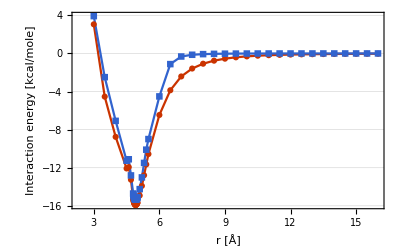
This script generates a plot for each dimer, plotting the minimum sampled energy configuration (in red) and the averaged interaction energy at a specific distance against the corresponding distance (refer to the example below).
To execute this script, copy and paste it to the ‘’Result’’ folder and run it. The plots will be saved in a directory named “Eij_plots”.

-Graphics-

```mathematica
ExportPlots[
dimerNameFolder_/;StringQ[dimerNameFolder],
outputFolder_/;StringQ[outputFolder]
]:=
Block[
{
data,
points,
dimerName,
plot
},
dimerName = FileNameSplit[dimerNameFolder]//Last;
data = Import [FileNameJoin[{dimerNameFolder,StringJoin[{dimerName,"_dist_vs_energy.dat" }]}]][[2;;]];
points ={{#[[1]],#[[2]]}&/@data, {#[[1]],#[[3]]}&/@data};
plot=ListLinePlot[
points,
Frame->{True,True,False,False},
FrameLabel->{
"r [Å]",
"Interaction energy [kcal/mole]"},
FrameStyle->Directive[Black],
PlotMarkers->Automatic,
LabelStyle->Directive[Bold],
PlotRange->All,
PlotRangePadding->Scaled[.05],
PlotTheme->{"Scientific", "VibrantColor", "HeightGrid"}(*,
PlotStyle->{RGBColor["#3277a8"],RGBColor["#4ecf13"]}*)
];
Export[FileNameJoin[{outputFolder,dimerName<>"_Eij_plot.png"}], plot, Background->None];
Export[FileNameJoin[{outputFolder,dimerName<>"_Eij_plot.svg"}], plot, Background->None]; 
]
SetDirectory[NotebookDirectory[]];
forceField = FileBaseName[FileNames[All,"IE",1]//Last];
results = Select[FileNames["*","IE/"<>forceField], DirectoryQ];
plotsDir = "Eij_plots";
If[
!DirectoryQ[plotsDir],
CreateDirectory[plotsDir];
];
Do[
subPlotDir = FileNameJoin[{plotsDir, results[[i]]}];
If[
!DirectoryQ[subPlotDir],
CreateDirectory[subPlotDir]
];
dimers=results[[i]];
ExportPlots[dimers,subPlotDir]
,{i, Length[results]}
];
```